```mathematica
ClearAll["Global`*"];
```

### Task & Variables

Modelling of Er fiber amplifier with raman pumping accounting for up-conversion and neglecting ESA. Pump @ 1480 nm, signal @ 1560 nm, input signal power P = 0.5 W, pump power 50 W, back pump

```mathematica
Ps0=0.5;
Pp0Left=0;
Pp0Right=50;
λp=1480×10^-9;
λs=1560×10^-9;
L=120;
c=3×10^8;
h=6.63×10^-34;
dcore=20×10^-6;
dclad=125×10^-6;
Nions=20×6.62×10^22;
τ=10×10^-3;
nref=1.45;
v=c/nref;
Cuc=4.5×10^-22;
```

```mathematica
σ12p=0.146×10^-24;
σ12s=0.105×10^-24;
σ21p=0.0264×10^-24;
σ21s=0.168×10^-24;
```

### Calculations

```mathematica
Aeffs=(π×dcore^2)/4;
Aeffp=(π×dcore^2)/4×2;
```

#### Rate equations for Er amplifier

```mathematica
ns=(Ps[z]×λs×nref)/(h×c^2×Aeffs);
npLeft=(PpLeft[z]×λp×nref)/(h×c^2×Aeffp);
npRight=(PpRight[z]×λp×nref)/(h×c^2×Aeffp);
```

```mathematica
N1N2=NSolve[0==v×(npLeft+npRight)×(σ12p×(Nions-N2[z])-σ21p×N2[z])+v×ns×(σ12s×(Nions-N2[z])-σ21s×N2[z])-N2[z]/τ-Cuc×(N2[z])^2,{N2[z]}][[2]];
N2[z_]=Evaluate[N2[z]/.N1N2[[1]]];
N1[z_]=Nions-N2[z];
```

```mathematica
sols=NDSolve[{D[PpLeft[z],z]==PpLeft[z]×(σ21p×N2[z]-σ12p×N1[z])×Aeffs/Aeffp,D[PpRight[z],z]==-PpRight[z]×(σ21p×N2[z]-σ12p×N1[z])×Aeffs/Aeffp,D[Ps[z],z]==Ps[z]×(σ21s×N2[z]-σ12s×N1[z]),PpLeft[0]==Pp0Left,PpRight[L]==Pp0Right,Ps[0]==Ps0},{PpLeft,PpRight,Ps},{z,0,L}]
```

{{PpLeft→InterpolatingFunction[…],PpRight→InterpolatingFunction[…],Ps→InterpolatingFunction[…]}}

Signal power distribution along the fiber

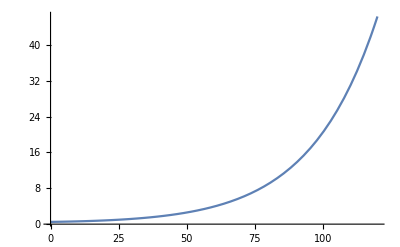

```mathematica
Plot[Ps[z]/.sols,{z,0,L},PlotRange->All]
```

Pump power distribution along the fiber

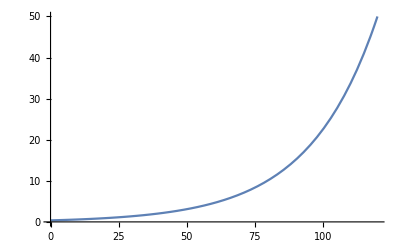

```mathematica
Plot[PpRight[z]/.sols,{z,0,L}]
```